```mathematica
"Refractive Index"
```

```mathematica
Subscript[n, 1]=1
Subscript[n, 2]=√10
Subscript[n, m]=√2
```

1

√10

√2

```mathematica
"Snell's Law, Fresnel Equation"
```

```mathematica
β=Β °
γ=Γ °
Subscript[n, 1] Sin[β]==Subscript[n, 2] Sin[γ]
Solve[Subscript[n, 1] Sin[β]==Subscript[n, 2] Sin[γ],Γ ]
γ=ArcSin[(Sin[β] Subscript[n, 1])/Subscript[n, 2]]
Subscript[r, s]=(Subscript[n, 1] Cos[β]-Subscript[n, 2] Cos[γ])/(Subscript[n, 1] Cos[β]+Subscript[n, 2] Cos[γ])
Subscript[r, p]=(Subscript[n, 2] Cos[β]-Subscript[n, 1] Cos[γ])/(Subscript[n, 1] Cos[γ]+Subscript[n, 2] Cos[β])
```

° Β

° Γ

Sin[° Β]==√10 Sin[° Γ]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Γ→ArcSin[Sin[° Β]/(√10)]/°}}

ArcSin[Sin[° Β]/(√10)]

(Cos[° Β]-√10 √(1-1/10 Sin[° Β]^2))/(Cos[° Β]+√10 √(1-1/10 Sin[° Β]^2))

(√10 Cos[° Β]-√(1-1/10 Sin[° Β]^2))/(√10 Cos[° Β]+√(1-1/10 Sin[° Β]^2))

```mathematica
"Plot"
```

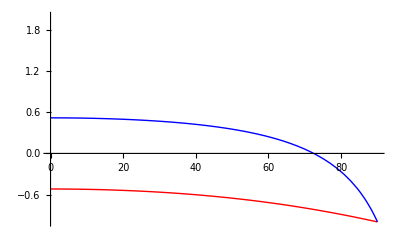

```mathematica
Plot[{Subscript[r, s],Subscript[r, p]},{Β, 0, 90},PlotRange->{-1,2},PlotStyle->{Red,Blue}]
```

```mathematica
"Fresnel Factor"
```

```mathematica
Subscript[L, xx]= (1-Subscript[r, p])Cos[β]
Subscript[L, yy]= 1+Subscript[r, s]
Subscript[L, zz]= (1+Subscript[r, p])Subscript[n, 1]^2/Subscript[n, m]^2 Sin[β]
```

Cos[° Β] (1-(√10 Cos[° Β]-√(1-1/10 Sin[° Β]^2))/(√10 Cos[° Β]+√(1-1/10 Sin[° Β]^2)))

1+(Cos[° Β]-√10 √(1-1/10 Sin[° Β]^2))/(Cos[° Β]+√10 √(1-1/10 Sin[° Β]^2))

1/2 Sin[° Β] (1+(√10 Cos[° Β]-√(1-1/10 Sin[° Β]^2))/(√10 Cos[° Β]+√(1-1/10 Sin[° Β]^2)))

```mathematica
Plot[{Subscript[r, s],Subscript[r, p]},{Β, 0, 90},PlotRange->{-1,2},PlotStyle->{Red,Blue}]
```

```mathematica
"Plot"
```

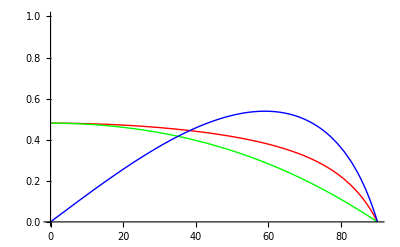

```mathematica
Plot[{Subscript[L, xx],Subscript[L, yy],Subscript[L, zz]},{Β, 0, 90},PlotRange->{0,1},PlotStyle->{Red,Green,Blue}]
```